{{1.53094,4},{1.61049,6},{1.67606,8},{1.73075,10},{1.78193,12},{1.82821,14},{1.87136,16},{1.91416,18},{1.9443,20},{1.98268,22.2},{2.00698,24},{2.03573,26},{2.06361,28},{2.08706,30},{2.11045,32},{2.13618,34},{2.15637,36},{2.17693,38},{2.17882,45},{2.18134,50},{2.1915,60},{2.18768,70},{2.18895,80},{2.19214,90},{2.19341,100},{2.2011,120},{2.20756,140},{2.21992,160},{2.23043,180},{2.24439,200},{2.25447,220}}

{{2.17693,38},{2.17882,45},{2.18134,50},{2.1915,60},{2.18768,70},{2.18895,80},{2.19214,90},{2.19341,100},{2.2011,120},{2.20756,140},{2.21992,160},{2.23043,180},{2.24439,200},{2.25447,220}}

FittedModel[-151.706+753.243/T]

FittedModel[-155.027+769.835/(0.0246869+T)]

| Estimate | Standard Error | t-Statistic | P-Value
C | 753.243 | 5.35434 | 140.679 | 1.93879×10^-31
U_0 | -151.706 | 2.43924 | -62.1941 | 2.29056×10^-24

| Estimate | Standard Error | t-Statistic | P-Value
C | 769.835 | 44.7269 | 17.2119 | 4.78592×10^-13
U_0 | -155.027 | 9.18241 | -16.8831 | 6.75825×10^-13
θ | -0.0246869 | 0.0657462 | -0.375489 | 0.711456

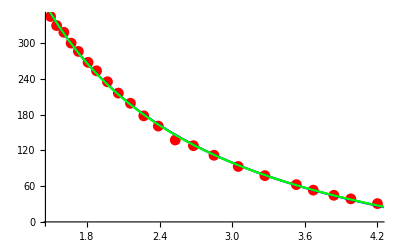

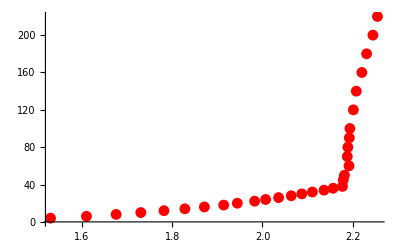

```mathematica
Filename = "abkuehlen"; 
Filepath = StringJoin[NotebookDirectory[], "../data/"]; 

rawData = Import[StringJoin[Filepath, Filename, ".txt"], "Table"] ;
partitionedData = Drop[rawData, 1][[All,{1,2}]];

aufwaermData = Import[StringJoin[Filepath, "aufwaermen", ".txt"], "Table"] ;
partitionedAufwaermData = Drop[aufwaermData, 1][[All,{1,2}]];
aufwaermTData = Map[{753.24/(#1[[2]]+151.71),#1[[1]]}&, partitionedAufwaermData]
vorLambda = Take[aufwaermTData,17]
nachLambda = Drop[aufwaermTData,17]

nlmCurie = NonlinearModelFit[partitionedData, C/T + Subscript[U, 0], {C, Subscript[U, 0]}, T]
nlmCurieWeiss=NonlinearModelFit[partitionedData, C/(T-θ) + Subscript[U, 0], {{C,700}, {Subscript[U, 0],-150},{θ,0}}, T]

nlmCurie["ParameterTable"]
nlmCurieWeiss["ParameterTable"]



Show[ListPlot[partitionedData, PlotStyle -> Red],Plot[{nlmCurieWeiss["BestFit"]},{T,1,5}, PlotStyle-> Blue], Plot[{nlmCurie["BestFit"]},{T,1,5}, PlotStyle-> Green]]
Show[ListPlot[aufwaermTData, PlotStyle -> Red]]
```

| Estimate | Standard Error | t-Statistic | P-Value
C | 769.835 | 44.7269 | 17.2119 | 4.78592×10^-13
U_0 | -155.027 | 9.18241 | -16.8831 | 6.75825×10^-13
θ | -0.0246869 | 0.0657462 | -0.375489 | 0.711456

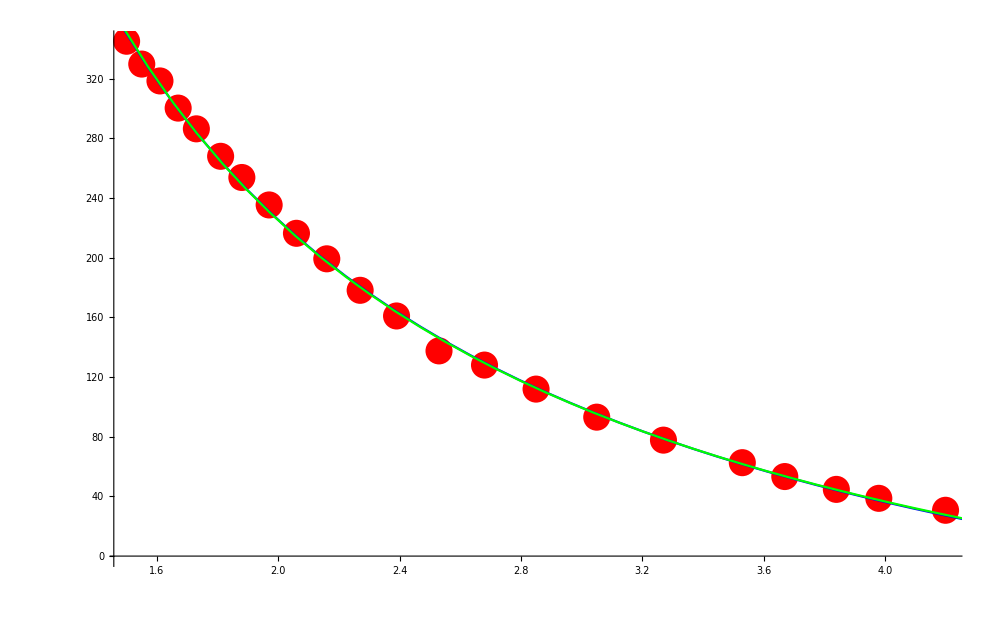

```mathematica
vorLambda = Drop[aufwaermTData,17]
```

```mathematica
nlmCurie["ParameterTable"]
```

```mathematica
nlmCurie
```